t^3

√t

t-0.00124551 t^2-0.162107 t^3

-0.00482216+1.02893 t-0.0591105 t^2-0.123529 t^3

-0.0754449+1.2408 t-0.270979 t^2-0.0529067 t^3

-0.353754+1.79742 t-0.642057 t^2+0.0295551 t^3

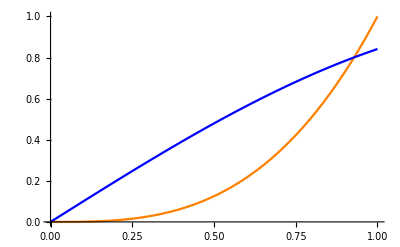

```mathematica
f[t_] = t^3
m[t_] = Sqrt[t]
g[t_] = (-0.162107*t^3)  -( 0.00124551*t^2)+t
h[t_] = (-0.123529*t^3)-(0.0591105*t^2)+(1.02893*t)-0.00482216
j[t_] = (-0.0529067*t^3)-(0.270979*t^2)+(1.2408*t)-0.0754449
k[t_] = (0.0295551*t^3)-(0.642057*t^2)+(1.79742*t)-0.353754
Show[{Plot[f[x],{x,0,1},PlotStyle->Orange],Plot[g[x],{x,0,0.5},PlotStyle->Blue],Plot[h[x],{x,0.5,1}, PlotStyle->Blue]},PlotRange->All, PlotLegends->{f[x],g[x],h[x]}]
(*Show[{Plot[f[x], {x, 1, 5}, PlotStyle->Red], Plot[m[x], {x, 1, 5}, PlotStyle->Blue]}, PlotRange->All]*)
```

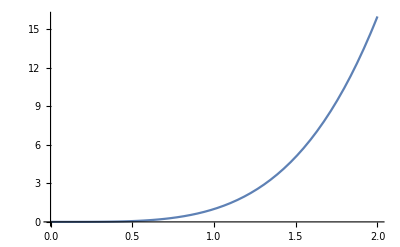

```mathematica
Show[%4,PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```